## Supplemental Material for: A Numerical Approach to Virasoro Blocks and the Information Paradox by Hongbin Chen, Charles Hussong, Jared Kaplan, and Daliang Li

This Mathematica notebooks contains the implementation of the Zamolochikov’s q recursion relation for the Virasoro blocks in 2D CFTs.  See the paper for references and further explanation.  This code can calculate the first 200 coefficients of the q-expansion in less than 10s, and for 1000 terms in about 45 mins. 

Tested in Mathematica version 11 for Mac OS X.

For the implementation of this algorithm using C++, please go to . The C++ code is somehow faster than this Mathematica code, and  the q-expansion coefficients used in the paper were obtained using the C++ code.

```mathematica
Date[][[1;;3]]
```

{2017,3,28}

### Recursion relation of Heavy-light Virasoro blocks

```mathematica
ClearAll["Global`*"]
```

```mathematica
Nprecision=300;(*Set precision*)
$MinPrecision=Nprecision;

(*qCoeffient returns the q-expansion coefficients. The inputs of qCoefficient[] are the the central charge cCentralCharge, light-operator dimension hLight, the heavy-operator dimension hHeavy, the intermediate operator dimension hIntermediate, and the highest power of the coefficients NN wanted.*)

qCoeffient[cCentralCharge_,hLight_,hHeavy_,hIntermediate_,NN_]:=Block[{c,hL,hH,b,h,countmn,lengthmn,startmn,Cij,CHij,λLsquare,λHsquare,λpq,Ppq,Rmn,RmnDenominator,RmnList,hmnList,mnhalfList,temp,NNhalf=Floor[NN/2],qCoefList=Table[0,Floor[NN/2]+1]},

(*NNhalf is number of terms in the list of the coefficients qCoefList that need to be calculated, since only even powers of q are non-zero.*)

(*Convert the arguments to high precision decimals. Do nothing for symbolic calculation.*)
hL=If[NumberQ[hLight],N[Rationalize[hLight],Nprecision],hLight];
hH=If[NumberQ[hHeavy],N[Rationalize[hHeavy],Nprecision],hHeavy];
c=If[NumberQ[cCentralCharge],N[Rationalize[cCentralCharge],Nprecision],cCentralCharge];
b=If[NumberQ[c],N[Rationalize[(√(c-13+√(c^2-26 c+25)))/(2 √3)],Nprecision],b];(*For symbolic calculation, present the result in terms of b.*)
h=If[NumberQ[hIntermediate],N[Rationalize[hIntermediate],Nprecision],hIntermediate];

λLsquare=1/4(b+1/b)^2-hL;(*Subscript[λ, L]^2*)
λHsquare=1/4(b+1/b)^2-hH;(*Subscript[λ, H]^2*)
λpq[p_,q_]:=1/2(p/b+q b);(*Subscript[λ, p,q]*)

Ppq[p_,q_]:=(λpq[p,q]^2-4λLsquare)(λpq[p,q]^2-4λHsquare ) λpq[p,q]^4;(*Ppq[p,q] gives the contribution to the numerator of Subscript[R, m,n] from Subscript[λ, p,q] and Subscript[λ, -p,-q]*)

RmnDenominator[m_,n_]:=Product[Piecewise[{{1,k==0&&l==0},{1,k==m&&l==n}},(k/b+l b)/2],{k,-m+1,m},{l,-n+1,n}];
(*RmnDenominator[m,n] give the denominator of Subscript[R, m,n], but only to be used for calculation of the first several terms of Subscript[R, m,n].*)

(*Subscript[R, m,n] is filled recursively from higher order terms, but we need to set the boundary values for this recursive calculation.*)
Rmn=Table[0,NN,NN];
Rmn[[1,2]]=2 Ppq[0,1]/RmnDenominator[1,2];
Rmn[[2,1]]=2 Ppq[1,0]/RmnDenominator[2,1];
Rmn[[2,2]]=2(Ppq[1,-1]Ppq[1,1])/RmnDenominator[2,2];
(*Obtain Subscript[R, m,1] and Subscript[R, m,2] from Subscript[R, m-2,1] and Subscript[R, m-2,2] respectively*)
Do[Rmn[[m,1]]=Rmn[[m-2,1]]/λpq[m-2,1] Ppq[m-1,0]λpq[m,1]Product[2/(k/b+nn b),{nn,0,1},{k,{-m+1,-m+2,m-1,m}}],{m,4,NN,2}];
Do[Rmn[[m,2]]=Rmn[[m-2,2]]/λpq[m-2,2] Ppq[m-1,-1]Ppq[m-1,1]λpq[m,2]Product[2/(k/b+nn b),{nn,-1,2},{k,{-m+1,-m+2,m-1,m}}],{m,3,NN}];
(*Obtain Subscript[R, m,n] from Subscript[R, m,n-2], only calculate terms with even mn*)
Do[Rmn[[m,n]]=If[OddQ[m n],0,Rmn[[m,n-2]]/λpq[m,n-2] λpq[m,n]Product[Ppq[p,n-1],{p,-m+1,m-1,2}]Product[2/(k/b+nn b),{nn,{-n+1,-n+2,n-1,n}},{k,-m+1,m}]],{m,1,NN},{n,3,NN/m}];

(*In the following calculation, Subscript[R, m,n] and Subscript[h, m,n] are stored into one-dimensional tables, and we only need to consider cases that mn is even*)

startmn=Table[0,Floor[NN/2]+1];
lengthmn=0;
Do[startmn[[i]]=lengthmn;lengthmn+=Length[Divisors[2i]],{i,1,NNhalf+1}];
lengthmn-=Length[Divisors[2(NNhalf+1)]];
(*lengthmn counts the length of these one-dimension tables, which is the sum of the number of divisors of even integers up to NN*)
(*Elements from startmn[[i]]+1 to startmn[[i+1]] of these one-dimensioanl tables to be defiend below  correspond to the Subscript[R, m,n] and Subscript[h, m,n] who have mn/2=i.*)  

RmnList=Table[0,lengthmn];
hmnList=Table[0,lengthmn];
mnhalfList=Table[0,lengthmn];

(*RmnList and hmnList are used to stores Subscript[h, m,n] and Subscript[R, m,n] into a one-dimensional tables. Those Subscript[h, m,n] s with the same product mn will be stored in hmnList from startmn[[mn/2]]+1 to startmn[[mn/2+1]], and similar for RmnList.*)
(*mnhalfList stores the number mn/2 that corresponds to the each element in these one-dimensional tables, for example mnhalfList[[1]]=1 ((1*2)/2==1), mnhalfList[[2]]=1 ((2*1)/2==1), mnhalfList[[3]]=2 ((1*4)/2==2), and so on*)

(*Below is how we construct these one-dimensional tables.*)
countmn=Table[0,NNhalf];
Do[If[EvenQ[m n],(temp=m n/2;countmn[[temp]]++;mnhalfList[[startmn[[temp]]+countmn[[temp]]]]=temp;RmnList[[startmn[[temp]]+countmn[[temp]]]]=Rmn[[m,n]];hmnList[[startmn[[temp]]+countmn[[temp]]]]=1/4(b+1/b)^2-λpq[m,n]^2),0],{m,1,NN},{n,1,NN/m}];
(*countmn[[temp]] records the number of divisors of 2temp that we encounters so far, so startmn[[temp]]+countmn[[temp]] is the position where the current element should be in these one-dimensional tables*)

HH=Table[Table[0,startmn[[i+1]]],{i,1,NNhalf}];(*HH[[i,j]] stores Subscript[H, m,n]^k in the diagonal way, as explained in the paper, where the fist index corresponds to the total power of Subscript[H, m,n]^k, which is i==(k+mn)/2 and the second index corresponds to (m,n). The length of HH[[i]] is startmn[[i+1]], which is the number of ways to write 2i as 2i==k+mn.*)

Do[HH[[i,j]]=1,{i,1,NNhalf},{j,startmn[[i]]+1,startmn[[i+1]]}];(*Subscript[H, m,n]^0=1*)

Cij=Table[RmnList[[j]]/(hmnList[[i]]+2mnhalfList[[i]]-hmnList[[j]]),{i,1,lengthmn},{j,1,startmn[[NNhalf-mnhalfList[[i]]+1]]}];(*Store the prefactors Subscript[C, ij]=Subscript[R, p,q]/(Subscript[h, m,n]+mn-Subscript[h, p,q]) into a two-dimensional table, where the first index corresponds to (m,n) and the second index corresponds to (p,q)*)

CHij=Table[RmnList[[i]]/(h-hmnList[[i]]),{i,1,lengthmn}];(*CHij is the list of prefactor to get the q-expansion coefficients in qCoefList, which are denoted as H^k in the paper*)

Do[Do[HH[[khalf+mnhalfList[[i]],i]]=Take[Cij[[i]],startmn[[khalf+1]]].HH[[khalf]],{i,1,startmn[[NNhalf-khalf+1]]}],{khalf,1,NNhalf}];
(*Calculate the Subscript[H, m,n]^k elements, this is the slow part of the code. The order that we conduct this calculation is that we calculate all the  Subscript[H, m,n]^k s with the same k, which can be obtained from HH[[k/2]], and then put them in the right places in HH[[]]. This process is explained in the Figure 19 of the paper.*)

qCoefList[[1]]=1;
Do[qCoefList[[i+1]]=Take[CHij,startmn[[i+1]]].HH[[i]],{i,1,NNhalf}];(*Construct the q-expansion coefficient H^k.*)
qCoefList]
```

### Examples

#### Example 1: c=30, h_L=1, h_H=3, h=0, N=1000

```mathematica
qCoeffient[30,1,3,0,1000]//N//AbsoluteTiming
```

{2645.94,{1.,1.7,29.6843,38.6386,333.155,342.276,2082.05,1763.41,8910.78,6486.56,29503.6,19003.6,81330.3,47378.3,195764.,104726.,424371.,210922.,847007.,394644.,1.58102×10^6,695443.,2.79255×10^6,1.16619×10^6,4.70856×10^6,1.87562×10^6,7.63264×10^6,2.91151×10^6,1.1959×10^7,4.38264×10^6,1.81926×10^7,6.42357×10^6,2.69668×10^7,9.19638×10^6,3.90685×10^7,1.2896×10^7,5.5455×10^7,1.77512×10^7,7.72901×10^7,2.40334×10^7,1.05957×10^8,3.2053×10^7,1.43108×10^8,4.21749×10^7,1.90669×10^8,5.48091×10^7,2.50908×10^8,7.04307×10^7,3.26425×10^8,8.95657×10^7,4.20249×10^8,1.12825×10^8,5.35811×10^8,1.40868×10^8,6.77058×10^8,1.74459×10^8,8.48412×10^8,2.14413×10^8,1.05493×10^9,2.61675×10^8,1.3022×10^9,3.17232×10^8,1.59659×10^9,3.8224×10^8,1.94507×10^9,4.57878×10^8,2.35552×10^9,5.45535×10^8,2.8365×10^9,6.46614×10^8,3.39767×10^9,7.62767×10^8,4.04939×10^9,8.95623×10^8,4.80338×10^9,1.04716×10^9,5.67207×10^9,1.21926×10^9,6.66945×10^9,1.41421×10^9,7.81032×10^9,1.6342×10^9,9.11133×10^9,1.88192×10^9,1.05898×10^10,2.15979×10^9,1.22654×10^10,2.47099×10^9,1.41585×10^10,2.81823×10^9,1.62918×10^10,3.20515×10^9,1.86889×10^10,3.63483×10^9,2.13766×10^10,4.11143×10^9,2.43817×10^10,4.63831×10^9,2.77351×10^10,5.22035×10^9,3.14676×10^10,5.86118×10^9,3.56146×10^10,6.5663×10^9,4.02113×10^10,7.33981×10^9,4.52979×10^10,8.1879×10^9,5.09142×10^10,9.11492×10^9,5.7106×10^10,1.01281×10^10,6.39182×10^10,1.1232×10^10,7.14024×10^10,1.24346×10^10,7.9609×10^10,1.37412×10^10,8.85964×10^10,1.51607×10^10,9.84202×10^10,1.66982×10^10,1.09146×10^11,1.83644×10^10,1.20837×10^11,2.01645×10^10,1.33565×10^11,2.21101×10^10,1.474×10^11,2.42072×10^10,1.62424×10^11,2.64686×10^10,1.78711×10^11,2.89×10^10,1.96354×10^11,3.15166×10^10,2.15436×10^11,3.43237×10^10,2.36057×10^11,3.73381×10^10,2.58308×10^11,4.05659×10^10,2.82303×10^11,4.40252×10^10,3.08138×10^11,4.77216×10^10,3.3594×10^11,5.16768×10^10,3.65814×10^11,5.58951×10^10,3.97898×10^11,6.04003×10^10,4.32308×10^11,6.51975×10^10,4.69195×10^11,7.03127×10^10,5.08682×10^11,7.57497×10^10,5.50938×10^11,8.1539×10^10,5.96096×10^11,8.76826×10^10,6.44336×10^11,9.4214×10^10,6.95806×10^11,1.01136×10^11,7.50702×10^11,1.08484×10^11,8.09179×10^11,1.16259×10^11,8.71455×10^11,1.24504×10^11,9.37695×10^11,1.33216×10^11,1.00813×10^12,1.42441×10^11,1.08295×10^12,1.52177×10^11,1.1624×10^12,1.62475×10^11,1.24667×10^12,1.73327×10^11,1.33605×10^12,1.84794×10^11,1.43072×10^12,1.96865×10^11,1.531×10^12,2.09604×10^11,1.63709×10^12,2.23×10^11,1.74933×10^12,2.37122×10^11,1.86793×10^12,2.51953×10^11,1.99325×10^12,2.67576×10^11,2.12553×10^12,2.83967×10^11,2.26515×10^12,3.01213×10^11,2.41235×10^12,3.1929×10^11,2.56757×10^12,3.38294×10^11,2.73104×10^12,3.58191×10^11,2.90322×10^12,3.79093×10^11,3.08439×10^12,4.00956×10^11,3.27502×10^12,4.239×10^11,3.47539×10^12,4.47883×10^11,3.68604×10^12,4.73031×10^11,3.90724×10^12,4.99287×10^11,4.13958×10^12,5.26805×10^11,4.38334×10^12,5.55511×10^11,4.63912×10^12,5.85567×10^11,4.90726×10^12,6.16902×10^11,5.18839×10^12,6.49687×10^11,5.48284×10^12,6.83832×10^11,5.79131×10^12,7.19541×10^11,6.11414×10^12,7.56703×10^11,6.45206×10^12,7.95531×10^11,6.80543×10^12,8.3592×10^11,7.17505×10^12,8.78092×10^11,7.56125×10^12,9.21915×10^11,7.96493×10^12,9.67659×10^11,8.38642×10^12,1.01516×10^12,8.82665×10^12,1.0647×10^12,9.28597×10^12,1.11612×10^12,9.76541×10^12,1.16972×10^12,1.02653×10^13,1.2253×10^12,1.07867×10^13,1.28321×10^12,1.133×10^13,1.34324×10^12,1.18962×10^13,1.40573×10^12,1.24859×10^13,1.47047×10^12,1.31002×10^13,1.53785×10^12,1.37394×10^13,1.60758×10^12,1.44049×10^13,1.68014×10^12,1.50971×10^13,1.75519×10^12,1.58172×10^13,1.83322×10^12,1.65657×10^13,1.91391×10^12,1.7344×10^13,1.99777×10^12,1.81525×10^13,2.08441×10^12,1.89928×10^13,2.17443×10^12,1.98652×10^13,2.26739×10^12,2.07714×10^13,2.36391×10^12,2.17117×10^13,2.46355×10^12,2.26879×10^13,2.56697×10^12,2.37003×10^13,2.67364×10^12,2.47509×10^13,2.78435×10^12,2.58398×10^13,2.89849×10^12,2.69692×10^13,3.01685×10^12,2.81393×10^13,3.13885×10^12,2.93523×10^13,3.26533×10^12,3.06084×10^13,3.3956×10^12,3.19099×10^13,3.53063×10^12,3.32571×10^13,3.66964×10^12,3.46523×10^13,3.81364×10^12,3.60957×10^13,3.96187×10^12,3.759×10^13,4.11536×10^12,3.91352×10^13,4.27322×10^12,4.07342×10^13,4.4367×10^12,4.23869×10^13,4.60476×10^12,4.40965×10^13,4.77867×10^12,4.58627×10^13,4.95745×10^12,4.7689×10^13,5.1424×10^12,4.9575×10^13,5.33236×10^12,5.15243×10^13,5.5289×10^12,5.35366×10^13,5.73068×10^12,5.56155×10^13,5.9393×10^12,5.77608×10^13,6.15349×10^12,5.99763×10^13,6.37486×10^12,6.22616×10^13,6.60196×10^12,6.46209×10^13,6.83672×10^12,6.70536×10^13,7.07745×10^12,6.9564×10^13,7.32613×10^12,7.21516×10^13,7.58114×10^12,7.48211×10^13,7.8445×10^12,7.75715×10^13,8.11435×10^12,8.0408×10^13,8.39308×10^12,8.33296×10^13,8.67857×10^12,8.63413×10^13,8.97327×10^12,8.94424×10^13,9.27513×10^12,9.26384×10^13,9.58663×10^12,9.59278×10^13,9.90545×10^12,9.93167×10^13,1.02345×10^13,1.02804×10^14,1.05713×10^13,1.06395×10^14,1.09186×10^13,1.10089×10^14,1.12739×10^13,1.13893×10^14,1.16404×10^13,1.17804×10^14,1.20151×10^13,1.21829×10^14,1.24016×10^13,1.25967×10^14,1.27967×10^13,1.30225×10^14,1.32039×10^13,1.34601×10^14,1.36201×10^13,1.39103×10^14,1.40491×10^13,1.43727×10^14,1.44873×10^13,1.48483×10^14,1.4939×10^13,1.53367×10^14,1.54003×10^13,1.58388×10^14,1.58754×10^13,1.63544×10^14,1.63607×10^13,1.68844×10^14,1.68605×10^13,1.74284×10^14,1.73705×10^13,1.79873×10^14,1.7896×10^13,1.85609×10^14,1.8432×10^13,1.91501×10^14,1.8984×10^13,1.97547×10^14,1.95471×10^13,2.03755×10^14,2.01269×10^13,2.10123×10^14,2.07179×10^13,2.16661×10^14,2.13265×10^13,2.23365×10^14,2.19468×10^13,2.30246×10^14,2.25852×10^13,2.37301×10^14,2.3236×10^13,2.44541×10^14,2.39056×10^13,2.5196×10^14,2.45877×10^13,2.59573×10^14,2.52898×10^13,2.67374×10^14,2.60047×10^13,2.75375×10^14,2.67401×10^13,2.83571×10^14,2.74892×10^13,2.91977×10^14,2.82596×10^13,3.00585×10^14,2.90436×10^13,3.09412×10^14,2.98503×10^13,3.1845×10^14,3.06711×10^13,3.27714×10^14,3.15151×10^13,3.37197×10^14,3.2374×10^13,3.46916×10^14,3.3257×10^13,3.56863×10^14,3.4155×10^13,3.67055×10^14,3.50786×10^13,3.77484×10^14,3.60174×10^13,3.88168×10^14,3.69825×10^13,3.99097×10^14,3.79639×10^13,4.10291×10^14,3.89725×10^13,4.2174×10^14,3.99972×10^13,4.33465×10^14,4.10509×10^13,4.45453×10^14,4.21212×10^13,4.57728×10^14,4.3221×10^13,4.70276×10^14,4.43384×10^13,4.83122×10^14,4.54865×10^13,4.96252×10^14,4.66522×10^13,5.0969×10^14,4.78503×10^13,5.23422×10^14,4.90664×10^13,5.37474×10^14,5.03156×10^13,5.51831×10^14,5.15841×10^13,5.6652×10^14,5.28868×10^13,5.81525×10^14,5.42084×10^13,5.96873×10^14,5.55665×10^13,6.12549×10^14,5.69441×10^13,6.28581×10^14,5.83586×10^13,6.44953×10^14,5.97939×10^13,6.61693×10^14,6.12677×10^13,6.78784×10^14,6.27617×10^13,6.96258×10^14,6.42966×10^13,7.14095×10^14,6.58524×10^13,7.32327×10^14,6.74494×10^13,7.50935×10^14}}

```mathematica
(*qCoeffientPublic[] returns a list of the q-expansion coefficients, starting from the coefficient of q^0, which is 1, and then that of q^2,q^4, etc. This list only includes coefficients of even powers q^(2n), since the coefficients of odd powers are zero.*)
```

#### Example 2: Analytic coefficients

```mathematica
(*The code can also be used to obtain the analytic coefficients of the q-expansion (the result is given in terms of b). But one should notice that the coefficients for hihger powers of q (like q^10) are pretty complicated.*)
```

```mathematica
qCoeffient[c,Subscript[h, L],Subscript[h, H],h,2]//AbsoluteTiming
```

{0.000907,{1,-(4 (1/(4 b^2)-4 (1/4 (1/b+b)^2-h_H)) (1/(4 b^2)-4 (1/4 (1/b+b)^2-h_L)))/(b^2 (-1/b+b) (1/b+b) (-1/4 (1/b+b)^2+1/4 (2/b+b)^2+h))-(4 b^2 (b^2/4-4 (1/4 (1/b+b)^2-h_H)) (b^2/4-4 (1/4 (1/b+b)^2-h_L)))/((1/b-b) (1/b+b) (-1/4 (1/b+b)^2+1/4 (1/b+2 b)^2+h))}}

#### Example 3: Plot the Heavy-Light Virasoro block

```mathematica
VBlock[c_,hL_,hH_,h_,N_]:=(16 q)^(h-(c-1)/24)z^((c-1)/24-2hL)(1-z)^((c-1)/24-hH-hL)EllipticTheta[3,0,q]^((c-1)/2-8(hH+hL))Table[q^i,{i,0,N,2}].qCoeffient[c,hL,hH,h,N]/.q->Exp[-π EllipticK[1-z]/EllipticK[z]];
```

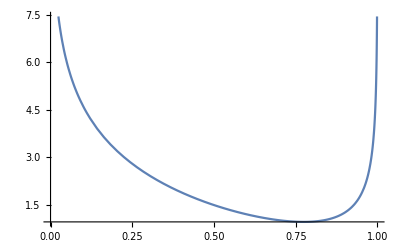

```mathematica
Plot[VBlock[30,1,3,0,10]//Log,{z,0,1}]
```

```mathematica
(*Series expansion*)
```

```mathematica
VBlock[c,hL,hH,0,2]/.b->(√(-13+c+√(25-26 c+c^2)))/(2 √3)//Series[#,{z,0,2}]&//Series[#,{c,Infinity,1}]&//Normal
```

z^(-2 hL) (1+(2 hH hL z^2)/c)

#### Example 4: Lorentzian time behavior of the Virasoro block

```mathematica
(*Analytic continuation to Lorentzian time*)
```

```mathematica
EK[r_,t_]:=EllipticK[1-r E^(-ⅈ t)]-2ⅈ (1+Floor[(-t-π)/(2π)]) EllipticK[r E^(-ⅈ t)];
qVal[r_,t_]:=Exp[-π EllipticK[r E^(-ⅈ t)]/EK[r,t]];
```

```mathematica
VBlockLorentzian[c_,hL_,hH_,h_,N_,r_]:=(16 q)^(h-(c-1)/24)z^((c-1)/24-2hL)(r)^((c-1)/24-hH-hL)E^(-ⅈ t ((c-1)/24-hH-hL))EllipticTheta[3,0,q]^((c-1)/2-8(hH+hL))Table[q^i,{i,0,N,2}].qCoeffient[c,hL,hH,h,N]/.{q->qVal[r,t],z->1-r E^(-ⅈ t)};
```

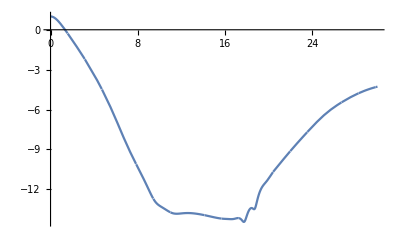

```mathematica
VBlockLorentzian[30,1,3,0,200,0.3]//Abs//Log;
Plot[%,{t,0,30}]
```